## How to use SMEFTsim, FeynArts and FeynCalc to obtain cross sections analytically

We start by loading FeynCalc and FeynArts before importing the model file “SMEFTsim_FA”.

```mathematica
Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"]
InstallFeynCalc[InstallFeynCalcDevelopmentVersion->True]
```

```mathematica
Quit[]
```

```mathematica
$LoadFeynArts=True;
<<FeynCalc`;
```

FeynCalc 10.0.0 (development version). For help, use the online documentation, check out the wiki or visit the forum.

Please check our FAQ for answers to some common FeynCalc questions and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
SetOptions[FourVector,FeynCalcInternal->False];
```

```mathematica
FAPatch[PatchModelsOnly->True]; (*important, see: http://www.feyncalc.org/forum/1600.html*)
```

Successfully patched FeynArts.

```mathematica
InitializeModel["dim_6_tt_parton", GenericModel -> "dim_6_tt_parton"];
```

loading generic model file /Users/jaco/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/dim_6_tt_parton.gen

> $GenericMixing is OFF

generic model {dim_6_tt_parton} initialized

loading classes model file /Users/jaco/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/dim_6_tt_parton.mod

> 49 particles (incl. antiparticles) in 22 classes

> $CounterTerms are ON

> 119 vertices

classes model {dim_6_tt_parton} initialized

For nicer drawings

```mathematica
MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
```

### qqbar -> t tbar

loading classes model file /Users/jaco/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/dim_6_tt_parton.mod

> 49 particles (incl. antiparticles) in 22 classes

> $CounterTerms are ON

> 119 vertices

classes model {dim_6_tt_parton} initialized

Excluding 0 Generic, 7 Classes, and 7 Particles fields

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 7 Classes, and 7 Particles fields

in total: 2 Classes insertions

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

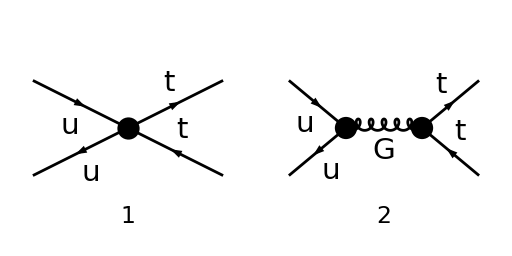

```mathematica
diagsqqtt=InsertFields[CreateTopologies[0,2->2],{F[3,{1}],-F[3,{1}]}->{F[30],-F[30]},InsertionLevel->{Classes},GenericModel -> "dim_6_tt_parton",Model->"dim_6_tt_parton",ExcludeParticles->{S[_],V[1|2]}];
Paint[diagsqqtt,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
diagsSM=InsertFields[CreateTopologies[0,2->2, ExcludeTopologies -> Irreducible],{F[3,{1}],-F[3,{1}]}->{F[30],-F[30]},InsertionLevel->{Classes},GenericModel -> "dim_6_8b",Model->"dim_6_8b",ExcludeParticles->{S[_],V[1|2]}];
Paint[diagsSM,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
diagsEFT=InsertFields[CreateTopologies[0,2->2, ExcludeTopologies -> Reducible],{F[3,{1}],-F[3,{1}]}->{F[30],-F[30]},InsertionLevel->{Classes},GenericModel -> "dim_6_8b",Model->"dim_6_8b",ExcludeParticles->{S[_],V[1|2]}];
Paint[diagsEFT,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];
```

#### Amplitude squared

```mathematica
repl = {SMP["g_s"]-> Subscript[g, s],gc27 -> -Subscript[g, s], gc28 ->  -Subscript[g, s], gc54-> 1/(6 * Λ^2),LambdaSMEFT -> Λ, vevhat-> v, ctu1-> 0, ctGIm-> 0, ctGRe-> 0, cuGIm-> 0, cuGRe-> 0};
```

```mathematica
CreateFeynAmp[diagsqqtt];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

in total: 2 Classes amplitudes

```mathematica
ampqqtt[0]=FCFAConvert[CreateFeynAmp[diagsqqtt],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,Contract->True,DropSumOver->True]/.repl
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

in total: 2 Classes amplitudes

-(g_s^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(OverBar[k_1],m_t)).(γ̄)^Lor1.(φ(-OverBar[k_2],m_t)) (φ(-OverBar[p_2],m_u)).(γ̄)^Lor1.(φ(OverBar[p_1],m_u)))/(OverBar[k_1]+OverBar[k_2])^2-((ctu8 δ_Col1Col3 δ_Col2Col4)/(2 Λ^2)-(ctu8 δ_Col1Col2 δ_Col3Col4)/(6 Λ^2)) (φ(OverBar[k_1],m_t)).(γ̄)^Ind178.(γ̄)^6.(φ(-OverBar[k_2],m_t)) (φ(-OverBar[p_2],m_u)).(γ̄)^Ind178.(γ̄)^6.(φ(OverBar[p_1],m_u))

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,SMP["m_u"],SMP["m_u"],SMP["m_t"],SMP["m_t"]];
```

```mathematica
ampqqttSquared[0]=Simplify[(TrickMandelstam[#1,{s,t,u,2*SMP["m_t"]^2}]&)[DiracSimplify[(FermionSpinSum[#1,ExtraFactor->1/2^2]&)[(SUNSimplify[#1,Explicit->True,SUNNToCACF->False]&)[FeynAmpDenominatorExplicit[(1/SUNN^2)*(ampqqtt[0]*ComplexConjugate[ampqqtt[0]])]]]]]];
```

```mathematica
ampqqttSquaredMassless[0]=(TrickMandelstam[#1,{s,t,u,2*SMP["m_t"]^2}]&)[(#1/.{SMP["m_u"]-> 0}&)[ampqqttSquared[0]]];
```

```mathematica
ampSquaredFullMasslessSUNN3[0]=ampqqttSquaredMassless[0]/.{SUNN-> 3}
```

-1/(162 Λ^4 s^2)(72 ctu8^2 s^2 u m_t^2-36 ctu8^2 s^2 m_t^4-36 ctu8^2 s^2 u^2-216 ctu8 Λ^2 s g_s^2 m_t^4+72 ctu8 Λ^2 s t g_s^2 m_t^2+216 ctu8 Λ^2 s u g_s^2 m_t^2-72 ctu8 Λ^2 s u^2 g_s^2-432 Λ^4 g_s^4 m_t^4+288 Λ^4 t g_s^4 m_t^2+288 Λ^4 u g_s^4 m_t^2-72 Λ^4 t^2 g_s^4-72 Λ^4 u^2 g_s^4)

Collect together terms involving the same power of 1/Λ^2

```mathematica
(*ampSquaredFinal = Collect[ampSquaredFullMasslessSUNN3[0], 1/Λ^2, Simplify]/.Λ^b_/;b<-4->0*)

dim6Sq = Collect[ampSquaredFullMasslessSUNN3[0]//Expand, 1/Λ^2, Simplify];
dim6Sm = dim6Sq/.{Λ^b_/;b≠0->0};
dim6Quad = (dim6Sq - dim6Sm)/.{Λ^b_/;b≠-4->0} ;
dim6Lin =(dim6Sq -  dim6Sm)/.{Λ^b_/;b≠-2->0} ;
```

```mathematica
ampSquaredFinal = {dim6Sm, dim6Lin, dim6Quad}
```

{(4 g_s^4 (-4 m_t^2 (t+u)+6 m_t^4+t^2+u^2))/(9 s^2),(4 ctu8 g_s^2 (-m_t^2 (t+3 u)+3 m_t^4+u^2))/(9 Λ^2 s),(2 ctu8^2 (u-m_t^2)^2)/(9 Λ^4)}

#### Cross section

```mathematica
prefac=1/(64 π^2 s)√(1-(4 SMP["m_t"]^2)/s);
diffXSection=prefac* Factor[ampSquaredFinal/.{t->SMP["m_t"]^2-s/2(1-√(1-(4 SMP["m_t"]^2)/s)Cos[θ]),u->SMP["m_t"]^2-s/2(1+√(1-(4 SMP["m_t"]^2)/s)Cos[θ]),Subscript[g, s]->(4*π*SMP["alpha_s"])^(1/2)}]
```

{(α_s^2 √(1-(4 m_t^2)/s) (-4 cos^2(θ) m_t^2+4 m_t^2+s cos^2(θ)+s))/(18 s^2),(ctu8 α_s √(1-(4 m_t^2)/s) (2 s cos(θ) √((s-4 m_t^2)/s)-4 cos^2(θ) m_t^2+4 m_t^2+s cos^2(θ)+s))/(144 π Λ^2 s),(ctu8^2 s √(1-(4 m_t^2)/s) (cos(θ) √((s-4 m_t^2)/s)+1)^2)/(1152 π^2 Λ^4)}

```mathematica
sigma = Integrate[2π*Sin[θ]*diffXSection, {θ, 0, π}, Assumptions->{Element[s, Reals], Element[SMP["m_t"], Reals], SMP["m_t"]> 0, s>4*SMP["m_t"]^2}]
```

{(8 π α_s^2 √(s-4 m_t^2) (2 m_t^2+s))/(27 s^(5/2)),(ctu8 α_s √(s-4 m_t^2) (2 m_t^2+s))/(27 Λ^2 s^(3/2)),(ctu8^2 (s-m_t^2) √(1-(4 m_t^2)/s))/(216 π Λ^4)}